# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Entropy\\Prethermalization\\Random state study\\QMB.wl"];
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[0,1]]+I RandomVariate[NormalDistribution[0,1]],{2^L}]];
(*haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[0,1]],{2^L}]];*)
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
Clear[statet];
statet[eigenval_,eigenvec_,transform_,t_,ini_]:=Module[{a,dim=Length[eigenval],inieigen=Conjugate[eigenvec].(Transpose[transform].ini)},
Chop[transform.Total[Exp[-I*eigenval*t]*inieigen*eigenvec]]
];
Clear[evensvn];
evensvn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,transform_,t_]:=Module[{state=statet[eigenval,eigenvec,transform,t,ini],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
cp=ResourceFunction["CombinePlots"];
```

```mathematica
Clear[rhoa];
rhoa[ini_,t_,L_,k_,val_,vec_]:=Module[{M,rhoc,rhob,rho,ck=Conjugate[vec] . ini,phases=arrayt[t,val,vec],perm=Delete[Range[L],{k}]},
MatrixPartialTrace[Dyad[N[Total[phases*ck]]],perm,2]
];
(*Clear[new];
new[ini_,t_,L_,k_,val_,vec_]:=Module[{ope=Pauli[3],rho=rhoa[ini,t,L,k,val,vec]},
Total[Map[VNentropy,(Chop[Eigenvalues[rho]])]]
];*)
Clear[sdiagonal];
sdiagonal[ini_,L_,k_]:=Module[{rho=Dyad[ini],perm=Delete[Range[L],{k}],rhoa},
rhoa=MatrixPartialTrace[Dyad[ini],perm,2];
Total[Map[VNentropy,(Chop[Eigenvalues[rhoa]])]]
];
```

```mathematica
Clear[rhoa];
rhoa[ini_,t_,L_,k_,val_,vec_]:=Module[{M,rhoc,rhob,rho,ck=Conjugate[vec] . ini,phases=arrayt[t,val,vec],perm=Delete[Range[L],{k}]},
MatrixPartialTrace[Dyad[N[Total[phases*ck]]],perm,2]
];
Clear[mag];
mag[L_,k_,ini_,t_,val_,vec_]:=Module[{ope=Pauli[3],rho=rhoa[ini,t,L,k,val,vec]},
Chop[Tr[rho.ope]]
];
Clear[vnentropy];
vnentropy[L_,k_,ini_,t_,val_,vec_]:=Module[{rho=rhoa[ini,t,L,k,val,vec]},
Total[Map[VNentropy,(Chop[Eigenvalues[rho]])]]
];
Clear[ClusterByWindow];
ClusterByWindow[energies_List,window_]:=Module[{e,s=Sort[energies],clusters={},curr,mn,mx},If[s==={},Return[{}]];
curr={First[s]};mn=mx=First[s];
Do[e=x;
If[Max[mx,e]-Min[mn,e]<=window,AppendTo[curr,e];mn=Min[mn,e];mx=Max[mx,e],AppendTo[clusters,curr];curr={e};mn=mx=e],{x,Rest[s]}];
AppendTo[clusters,curr];
clusters];
```

```mathematica
Clear[arrayt];
arrayt[t_,val_,vec_]:=Exp[-I*val*t]*vec;
Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{phases=arrayt[t,eigenval,eigenvec],rho,dima=2^(La),dimb=2^(Lb),ck=Conjugate[eigenvec] .ini},
rho=MatrixPartialTrace[Dyad[N[Total[ phases*ck]]],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
```

```mathematica
Clear[new];
(*new[L_,la_,lb_,ini_,val_,vec_,t_]:=Module[{schmidt,psit,ck=Conjugate[vec] . ini,a=2^(la),b=2^(lb),phases=Chop[arrayt[t,val]]*vec},
psit=ArrayReshape[N[Total[ phases*ck]],{a,b}];
Total[Map[VNentropy,Quiet[(Chop[SingularValueList[psit]])^2]]]
];*)
```

```mathematica
Clear[new];
new[L_,eigenval_,eigenvec_,ini_,t_]:=Module[{schmidt,psit,ck=Conjugate[eigenvec] . ini,d=2^(L/2),phases=arrayt[t,eigenval,eigenvec]},
psit=ArrayReshape[N[Total[ck*phases]],{d,d}];
Total[Map[VNentropy,(Chop[SingularValueList[psit]])^2]]
];
```

# Random states

```mathematica
J=1;
g=1;
tlist=Table[10^i,{i,-1,12,0.0040}];
tlist//Length
```

3251

```mathematica
hlist=Table[10^i,{i,-6,-1,0.5}];
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
hlist//Length
```

11

```mathematica
L=8;
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
```

```mathematica
L=8;
dim=2^L; (*Dimension of the Hilbert space*)
basisStates=IntegerDigits[Range[0,dim-1],2,L];
TranslateState[state_List]:=RotateLeft[state];
orbits={};
visited=Association[];
Do[If[!KeyExistsQ[visited,state],orbit=NestList[TranslateState,state,L-1];
orbit=DeleteDuplicates[orbit];
(*Mark all states in the orbit as visited*)Scan[(visited[#]=True)&,orbit];
AppendTo[orbits,orbit];],{state,basisStates}];
(*Creating momentum states*)
momentumEigenstates={};
Do[orbitSize=Length[orbit];
Do[k=2 Pi m/orbitSize;
stateSum=ConstantArray[0,dim];
Do[translatedState=Nest[TranslateState,orbit[[1]],n];
index=Position[basisStates,translatedState][[1,1]];
stateSum[[index]]+=Exp[-I k n];,{n,0,orbitSize-1}];
normalizedState=stateSum/Norm[stateSum];
AppendTo[momentumEigenstates,{k,normalizedState}];,{m,0,orbitSize-1}];,{orbit,orbits}];
(*Sorting everything*)
ks=First/@momentumEigenstates;
perm=OrderingBy[momentumEigenstates,First];
sortedKEigen=ks[[perm]];
sortedStates=(Last/@momentumEigenstates)[[perm]];
sortedPairs=Transpose[{sortedKEigen,sortedStates}];
dimensions=Tally[sortedKEigen];
```

```mathematica
allvalues={};
allvectors={};
Do[

H=IsingNNClosedHamiltonian[1,hlist[[h]],J,L];
U=Transpose[sortedStates];
HMomentumBasis=ConjugateTranspose[U].H.U;
posByK=GroupBy[Range@Length[sortedKEigen],sortedKEigen[[#]]&];
blocks={};
Do[
AppendTo[blocks,HMomentumBasis[[i[[1]];;i[[-1]],i[[1]];;i[[-1]]]]];
,{i,posByK}];
eigen=ParallelTable[Eigensystem[i],{i,blocks},DistributedContexts->Full];
transforms=Table[Transpose[Chop[sortedStates[[i]]]],{i,posByK}];
eigenvecs={};
Do[
a=ParallelTable[Chop[transforms[[j]].i],{i,eigen[[j,2]]},DistributedContexts->Full];
AppendTo[eigenvecs,a];
,{j,Length[transforms]}];
allvecs=Flatten[eigenvecs,1];
allvals=Flatten[Chop[eigen[[All,1]]]];

AppendTo[allvalues,allvals];
AppendTo[allvectors,allvecs];

,{h,Length[hlist]}];
```

```mathematica
allvalues={};
allvectors={};

Do[

H=IsingNNOpenHamiltonian[hlist[[h]],1,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];

AppendTo[allvalues,allvals];
AppendTo[allvectors,allvecs];

,{h,Length[hlist]}];
```

```mathematica
statee=Flatten[KroneckerProduct[haar[4],haar[4]]];
statef=RandomChainProductState[L];
productstatesfull={statee,statef};
```

```mathematica
productstatesfull={};
allstates=Table[RandomChainProductState[L],1000];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvectors[[1]]].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{1/iprs,allstates}],First];
AppendTo[productstatesfull,data[[All,2]][[-1]]];

allstates=Table[Flatten[KroneckerProduct[haar[4],haar[4]]],1000];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvectors[[1]]].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{1/iprs,allstates}],First];
AppendTo[productstatesfull,data[[All,2]][[-1]]];
```

```mathematica
allplots={};
Do[

(*HALF ENTROPY*)
(*entropy=ParallelTable[svn[L,3,3,j,allvalues[[h]],allvectors[[h]],t],{j,productstatesfull},{t,tlist},DistributedContexts->Full];*)
entropy=ParallelTable[new[L,allvalues[[h]],allvectors[[h]],j,t],{j,productstatesfull},{t,tlist},DistributedContexts->Full];

plots=Table[Show[{ListLogLinearPlot[{Transpose[{tlist,entropy[[q]]}],MovingAverage[Transpose[{tlist,entropy[[q]]}],200]},PlotStyle->{Directive[Gray,Opacity[0.10]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->800,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["PBC, L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1",35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}],LogLinearPlot[{pageEntropy[1,7],pageEntropy[2,6],pageEntropy[3,5],pageEntropy[4,4]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Gray,Dashed],Directive[Orange,Dashed],Directive[Brown,Dashed],Directive[Purple,Dashed],Directive[Blue,Dashed]}]},PlotRange->{All,{0,pageEntropy[4,4]}}],{q,2}];

AppendTo[allplots,plots];

,{h,Length[hlist]}];
```

```mathematica
Show[allplots[[All,1]],PlotRange->All]
Show[allplots[[All,2]],PlotRange->All]
```

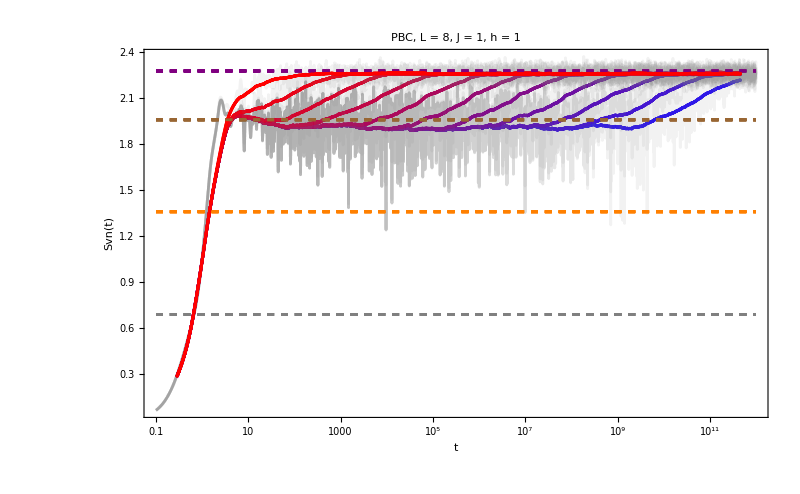

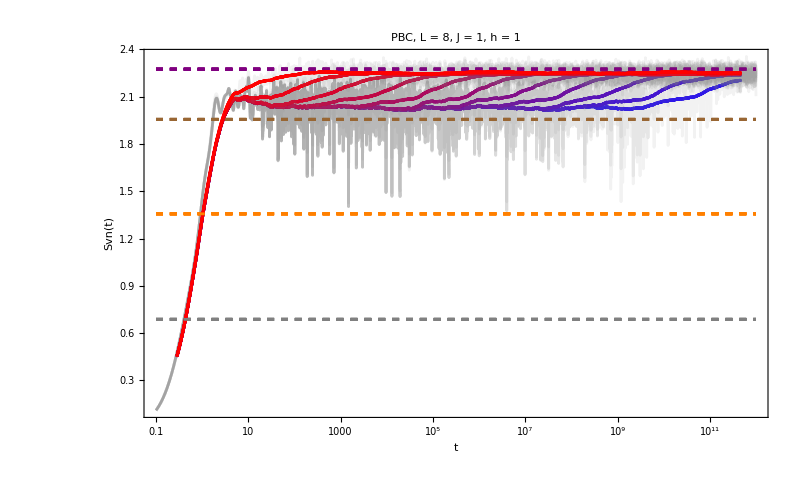

```mathematica
Show[allplots[[All,1]],PlotRange->All]
Show[allplots[[All,2]],PlotRange->All]
```

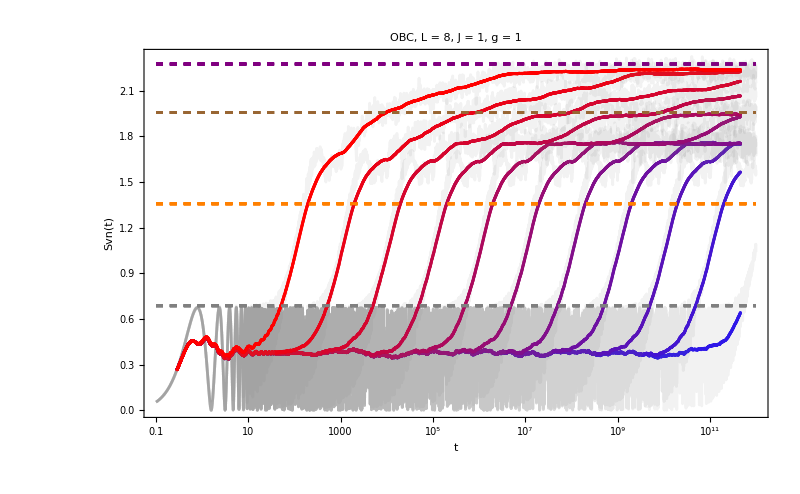

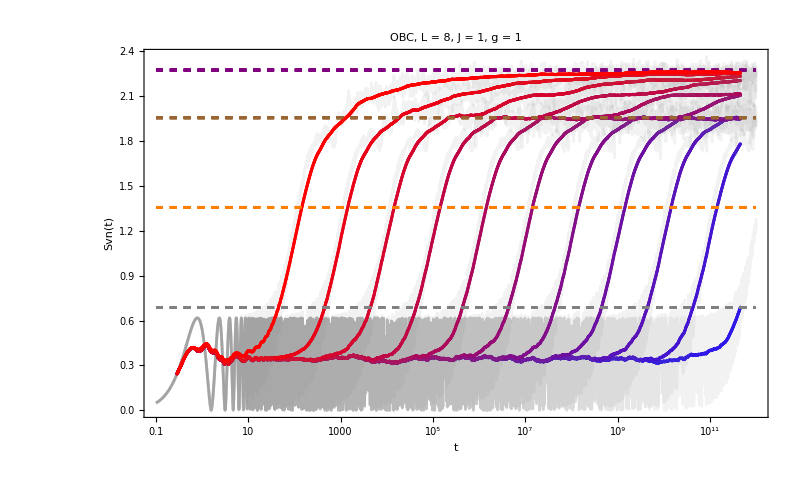

```mathematica
Show[allplots[[All,1]],PlotRange->All]
Show[allplots[[All,2]],PlotRange->All]
```

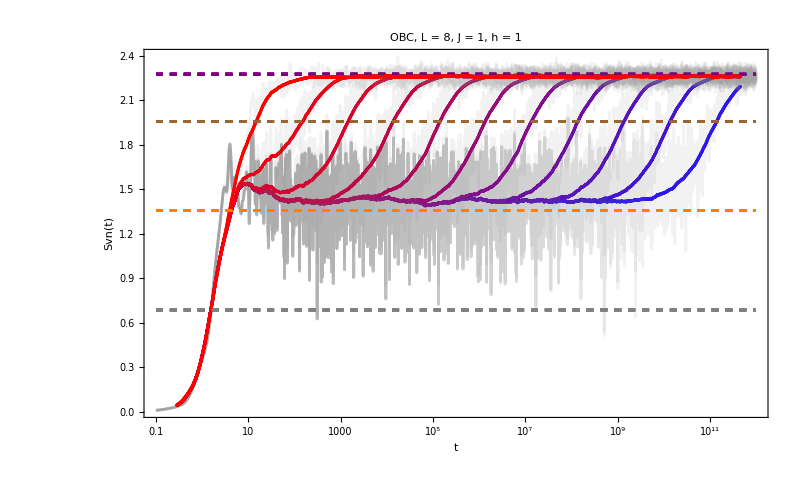

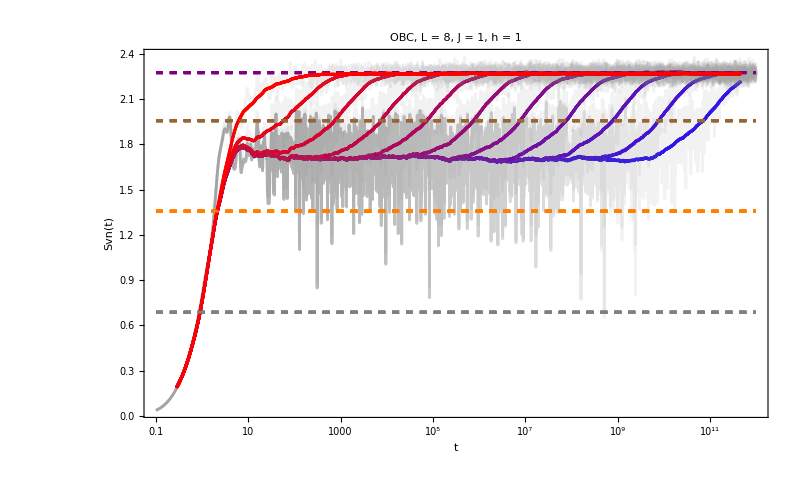

```mathematica
Show[allplots[[All,1]],PlotRange->All]
Show[allplots[[All,2]],PlotRange->All]
```

## L = 6

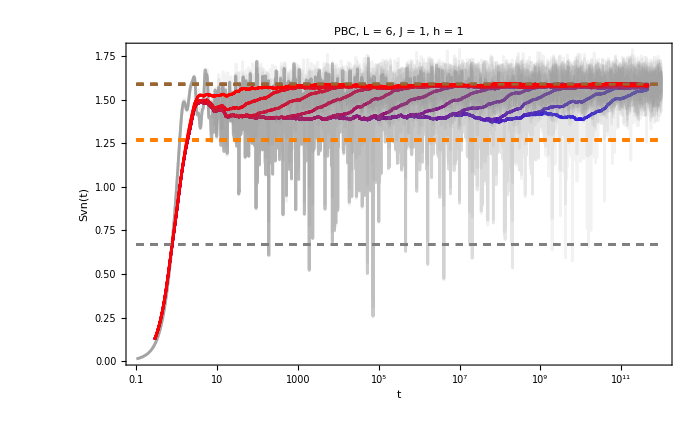

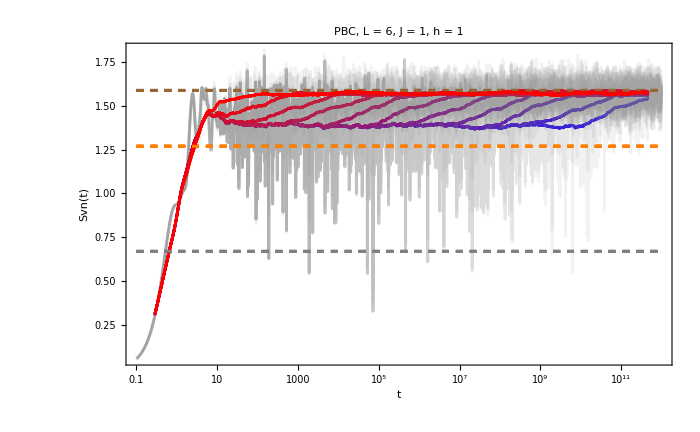

```mathematica
Show[allplots[[All,1]],PlotRange->All]
Show[allplots[[All,2]],PlotRange->All]
```

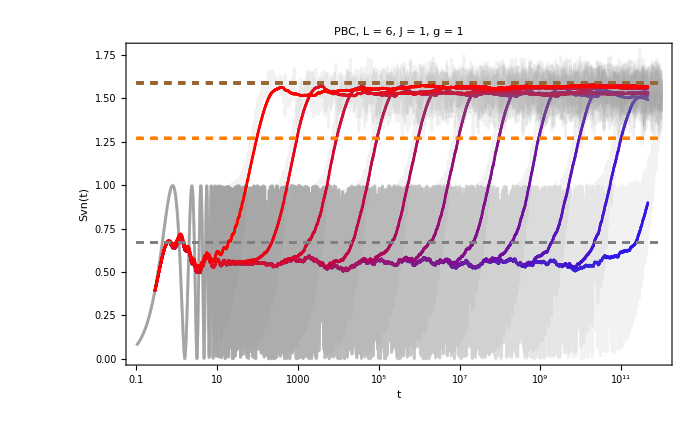

```mathematica
Show[allplots[[All,1]],PlotRange->All]
Show[allplots[[All,2]],PlotRange->All]
```

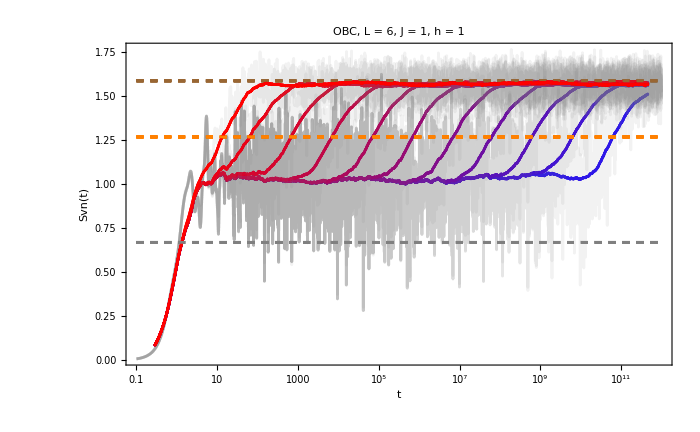

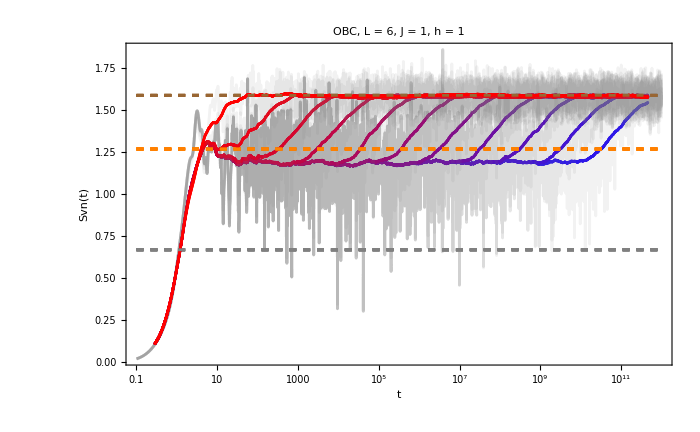

```mathematica
Show[allplots[[All,1]],PlotRange->All]
Show[allplots[[All,2]],PlotRange->All]
```

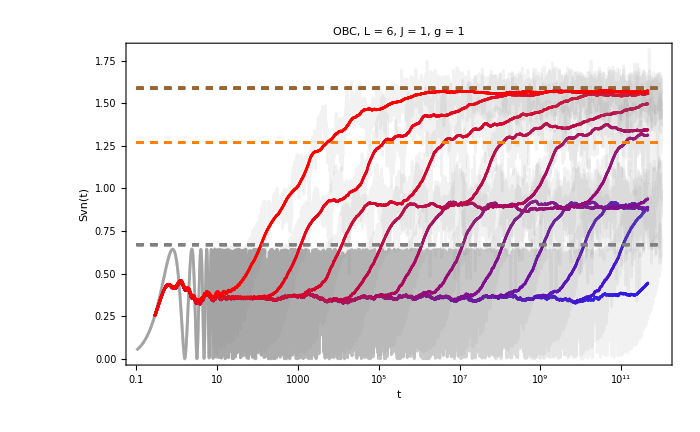

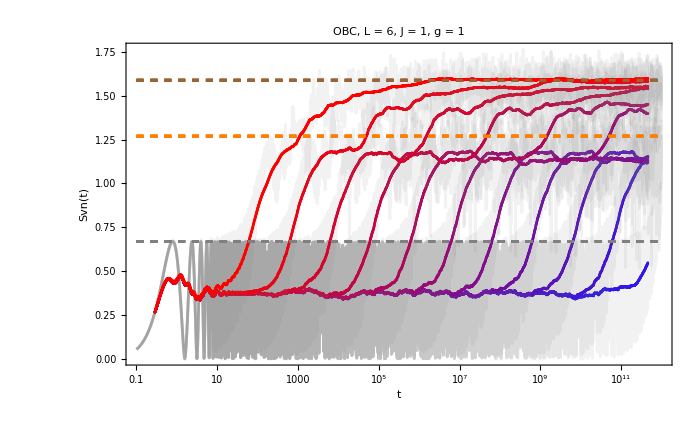

```mathematica
Show[allplots[[All,1]],PlotRange->All]
Show[allplots[[All,2]],PlotRange->All]
```